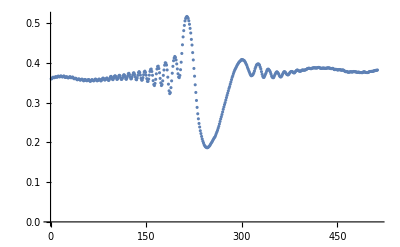

```mathematica
expImage = -Graphics-;
grayImage=ColorConvert[expImage,"Grayscale"];
intensVals=Mean[ImageData[grayImage]];
ListPlot[intensVals, PlotRange->All]
```